# Neural Networks

## NetTrain

Define a single-layer neural network that takes in scalar numeric values and produces scalar numeric values:

```mathematica
net=DotPlusLayer[1, "Input"->"Scalar", "Output"-> "Scalar"]
```

DotPlusLayer[…]

```mathematica
trained = NetTrain[net, {1->8, 2->19, 3->28, 4-> 37}]
```

None

```mathematica
trained[2.4]
```

22.04

```mathematica
trained[{1,2,3,4}]
```

{8.60003,18.2,27.8,37.4}

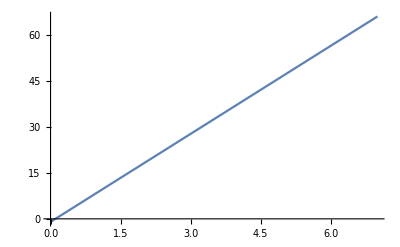

```mathematica
Plot[trained[x],{x,0,7}]
```

Define a network that takes in scalar numeric values and produces vectors of length two that are used as probabilities for the classes True and False:

```mathematica
net= NetChain[{DotPlusLayer[2], SoftmaxLayer[2]},
	"Input"->"Scalar", "Output"-> NetDecoder[{"Class", {True, False}}]]
```

NetChain[]

```mathematica
trained = NetTrain[net, {1 -> False, 2-> False, 3-> True, 4-> True}]
```

NetChain[]

```mathematica
trained [3.5]
```

True

```mathematica
trained[Range[10]]
```

{False,False,True,True,True,True,True,True,True,True}

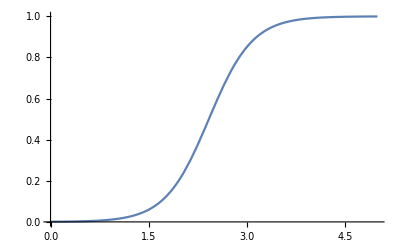

```mathematica
Plot[trained[x,{"Probability", True}], {x, 0, 5}]
```

```mathematica
net = NetChain[{32, Tanh, 1}, "Input" ->2, "Output"->"Scalar"]
```

Define a three-layer network that takes in vectors of length two and produces scalar numeric values:

NetChain[]

```mathematica
trainingData = Flatten[Table[{x,y}->x*y,{x,-1,1,.005}, {y, -1,1,.005}]];
```

```mathematica
trained = NetTrain[net, trainingData, BatchSize->1024]
```

NetChain[]

```mathematica
Plot3D[trained[{x,y}],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

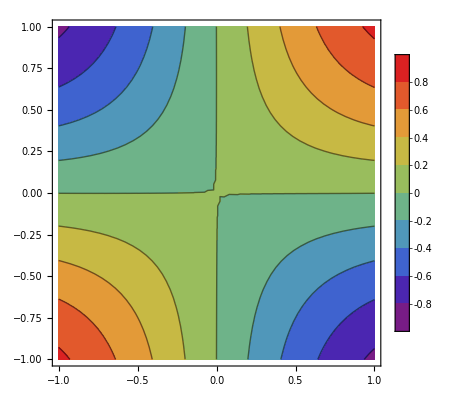

```mathematica
ContourPlot[trained[{x,y}],{x,-1,1},{y,-1,1},
	ColorFunction->"Rainbow", PlotLegends->Automatic]
```

# Loss Specifications

Train a simple net using MeanSquaredLossLayer

```mathematica
net = DotPlusLayer["Input"-> "Scalar", "Output"-> "Scalar"];
data = {1->1.9, 2->4.1, 3-> 6.0, 4-> 8.1};
trained = NetTrain[net, data]
```

None

```mathematica
trained[Range[4]]
```

{1.95001,4.,6.05,8.09999}

```mathematica
loss = MeanAbsoluteLossLayer["Target"-> "Scalar"]
```

MeanAbsoluteLossLayer[…]

```mathematica
loss[<|"Input"->5.0, "Target" -> 3.0|>]
```

2.

```mathematica
data = {1 -> 1.9, 2 -> 4.1, 3 -> 6.0, 4 -> 8.1};
trained = NetTrain[net, data, loss]
```

None

```mathematica
trained[Range[4]]
```

{1.89999,3.96665,6.03331,8.09997}

# Options

## BatchSize

### ?

```mathematica
trainingData = 
  RandomReal[1, {10000, 4}] -> RandomReal[1, {10000, 4}];
net = NetChain[{DotPlusLayer[8], DotPlusLayer[4]}, "Input" -> 4];
NetTrain[net, trainingData, BatchSize -> 512, 
   MaxTrainingRounds -> 20]; // AbsoluteTiming
```

{0.236011,Null}

## MaxTrainingRounds

```mathematica
trainingData = 
  RandomReal[1, {10000, 4}] -> RandomReal[1, {10000, 4}];
net = NetChain[{8, 4}, "Input" -> 4];
NetTrain[net, trainingData, MaxTrainingRounds -> 1]
```

NetChain[]

## Method

Stochastic Gradient Decent

```mathematica
dotPlus = DotPlusLayer[1,"Input"-> "Scalar", "Output"-> "Scalar"]
```

DotPlusLayer[…]

```mathematica
data = {1 -> 2.2, 2 -> 3.8, 3 -> 6.4, 4 -> 9.1};
```

```mathematica
net = NetTrain[dotPlus, data, Method -> "StochasticGradientDescent"]
```

None

```mathematica
net = NetTrain[dotPlus, data, 
  Method -> {"StochasticGradientDescent", 
    "InitialLearningRate" -> 0.1}]
```

None

Use regularization to prevent overfitting. Create synthetic training data based on a Gaussian curve:

```mathematica
data = Table[
   x -> Exp[-x^2] + RandomVariate[NormalDistribution[0, .15]], {x, -3,
     3, .2}];
```

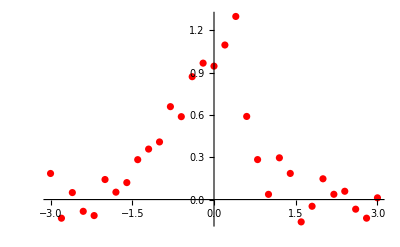

```mathematica
plot = ListPlot[List @@@ data, PlotStyle -> Red]
```